# Calculating the vev of σ and particle masses.

```mathematica
fπ=1000
```

1000

```mathematica
m2σ[σ]:=-m^2-c/(F n)(F/n-1)σ^(F/n-2)+3/2 λ σ^2 
m2η[σ]:=-m^2+c/(F n)(F/n-1)σ^(F/n-2)+1/2 λ σ^2 
m2π[σ]:=-m^2-c/F σ^(F/n-2)+1/2 λ σ^2 
m2X[σ]:=-m^2+c/F σ^(F/n-2)+1/2(λ+2λA ) σ^2
```

#### F/N = 1

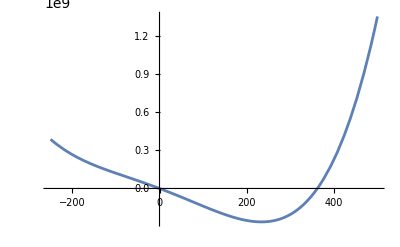

```mathematica
Plot[-m^2/2 σ^2-c/F^2 σ+λ/8 σ^4/.{F->3,c->+11684210.52631579,λ->0.29894736842105263,λA->0.015157894736842136,m^2->2631.57894736842,m^6->2631.57894736842^3,n->3},{σ,-250,500}]
```

```mathematica
veva=Solve[-m^2 σ-c/F^2+λ/2 σ^3==0,σ]//FullSimplify
```

{{σ→(2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))/(3^(2/3) F^2 λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(1/3))},{σ→(-2 (-3)^(1/3) F^4 m^2 λ+(-1)^(2/3) (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))/(3^(2/3) F^2 λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(1/3))},{σ→(4 (-3)^(2/3) F^4 m^2 λ-2 (-3)^(1/3) (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))/(6 F^2 λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(1/3))}}

```mathematica
N[veva[[1]][[1]]/.{F->3,c->1000,λA->2/3,λ->.3+2/3,m^2->481^2,m^6->481^6,n->1}]
```

σ→691.866-2.51287×10^-13 ⅈ

```mathematica
a1=m2σ[σ]/.{n->F,veva[[1]][[1]]}
```

-m^2+((2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))^2)/(2 3^(1/3) F^4 λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))

```mathematica
a1a=m2σ[σ]/.n->F
```

-m^2+(3 λ σ^2)/2

```mathematica
a2=m2η[σ]/.{n->F,veva[[1]][[1]]}
```

-m^2+((2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))^2)/(6 3^(1/3) F^4 λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))

```mathematica
a2a=m2η[σ]/.n->F
```

-m^2+(λ σ^2)/2

```mathematica
a3=m2π[σ]/.{F/n->1,veva[[1]][[1]]}
```

-m^2-(3^(2/3) c F λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(1/3))/(2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))+((2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))^2)/(6 3^(1/3) F^4 λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))

```mathematica
a3a=m2π[σ]/.{F/n->1}
```

-m^2-c/(F σ)+(λ σ^2)/2

```mathematica
a4=m2X[σ]/.{n->F,veva[[1]][[1]]}
```

-m^2+(3^(2/3) c F λ (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(1/3))/(2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))+((2 3^(1/3) F^4 m^2 λ+(9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))^2 (λ+2 λA))/(6 3^(1/3) F^4 λ^2 (9 c F^4 λ^2+√3 √(F^8 λ^3 (-8 F^4 m^6+27 c^2 λ)))^(2/3))

```mathematica
a4a=m2X[σ]/.n->F
```

-m^2+c/(F σ)+1/2 (λ+2 λA) σ^2

```mathematica
(a3a+a4a-2a2a)//Simplify
```

λA σ^2

```mathematica
Solve[a1s==a1&&a2s==a2&&a3s==a3&&a4s==a4, {c,λ,λA,m}]
```

{}

### F/N = 2

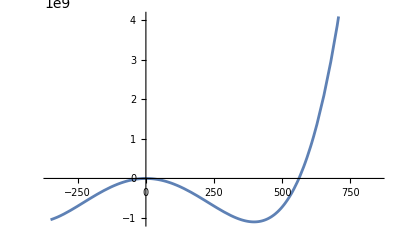

```mathematica
Plot[-m^2/2 σ^2-c/F^2 σ^2+λ/8 σ^4/.{m->√25776.31578947368,λ->0.35257894736842105,c->36592.1052631579,F->6},{σ,-350,850}]
```

```mathematica
vevb=Solve[-m^2-(c n)/F σ^0+λ/2 σ^2==0,σ]//FullSimplify
```

{{σ→-(√2 √(F m^2+c n))/(√F √λ)},{σ→(√2 √(F m^2+c n))/(√F √λ)}}

```mathematica
b1=m2σ[σ]/.vevb[[2]][[1]]/.n->F/2//Simplify
```

c (3/2-2/F^2)+2 m^2

```mathematica
b2=m2η[σ]/.vevb[[2]][[1]]/.n->F/2//Simplify
```

c (1/2+2/F^2)

```mathematica
b3=m2π[σ]/.vevb[[2]][[1]]/.n->F/2//Simplify
```

(c (-2+F))/(2 F)

```mathematica
b4=m2X[σ]/.vevb[[2]][[1]]/.n->F/2//Simplify
```

(2 m^2 λA)/λ+c (1/2+1/F+λA/λ)

```mathematica
b1+b2//Simplify
```

2 (c+m^2)

```mathematica
b2+b3//Simplify
```

(c (2-F+F^2))/F^2

#### F/N = 3

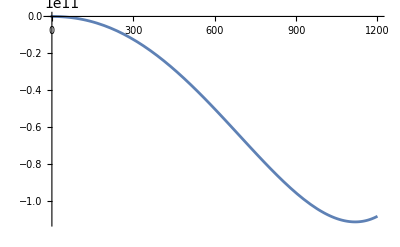

```mathematica
Plot[-m^2/2 σ^2-c/F^2 σ^3+λ/8 σ^4/.{F->3,c->1000,λA->2/3,λ->.3+2/3,m^2->481^2,m^6->481^6,n->1},{σ,-5,1200}]
```

```mathematica
vevc=Solve[-m^2-(c n)/F σ^1+λ/2 σ^2==0,σ]//FullSimplify
```

{{σ→(c n-√(c^2 n^2+2 F^2 m^2 λ))/(F λ)},{σ→(c n+√(c^2 n^2+2 F^2 m^2 λ))/(F λ)}}

```mathematica
N[vevc[[2]][[1]]/.{F->3,c->1000,λA->2/3,λ->.3+2/3,m^2->481^2,m^6->481^6,n->1}]
```

σ→1117.86

```mathematica
c1=m2σ[σ]/.vevc[[2]][[1]]/.n->F/3//Simplify
```

(c^2 F (-6+F^2)+6 F^3 m^2 λ+c (-6+F^2) √(F^2 (c^2+18 m^2 λ)))/(3 F^3 λ)

```mathematica
c2=m2η[σ]/.vevc[[2]][[1]]/.n->F/3//Simplify
```

(c (18+F^2) (c F+√(F^2 (c^2+18 m^2 λ))))/(9 F^3 λ)

```mathematica
c3=m2π[σ]/.vevc[[2]][[1]]/.n->F/3//Simplify
```

(c (-3+F) (c F+√(F^2 (c^2+18 m^2 λ))))/(9 F^2 λ)

```mathematica
c4=m2X[σ]/.vevc[[2]][[1]]/.n->F/3//Simplify
```

1/(18 F^2 λ^2)(9 F^2 λ (λ^2-2 m^2 (λ-2 λA))+2 c^2 F (3 λ+2 F λA)+2 c √(F^2 (c^2+18 m^2 λ)) (3 λ+2 F λA))

#### F/N = 4

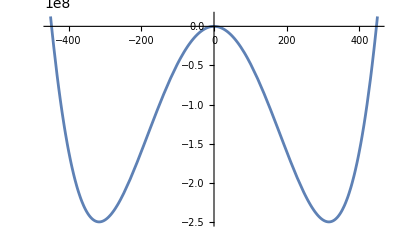

```mathematica
Plot[-m^2/2 σ^2-c/F^2 σ^4+λ/8 σ^4/.{m->100,λ->1,c->.1,F->1},{σ,-450,450}]
```

```mathematica
Solve[-m^2-(c n)/F σ^2+λ/2 σ^2==0,σ]//FullSimplify
```

{{σ→-(2 m)/(√(-(4 c n)/F+λ))},{σ→(2 m)/(√(-(4 c n)/F+λ))}}

#### F/N = 5

```mathematica
Solve[-m^2-(c n)/F σ^3+λ/2 σ^2==0,σ]//FullSimplify
```

{{σ→-((864 c^2 F m^2 n^2-F^3 λ^3+24 √(1296 c^4 F^2 m^4 n^4-3 c^2 F^4 m^2 n^2 λ^3))^(1/3)+F λ (-1+(F λ)/((864 c^2 F m^2 n^2-F^3 λ^3+24 √(1296 c^4 F^2 m^4 n^4-3 c^2 F^4 m^2 n^2 λ^3))^(1/3))))/(12 c n)},{σ→(2 F λ+((1+ⅈ √3) F^2 λ^2)/((864 c^2 F m^2 n^2-F^3 λ^3+24 √(1296 c^4 F^2 m^4 n^4-3 c^2 F^4 m^2 n^2 λ^3))^(1/3))+(1-ⅈ √3) (864 c^2 F m^2 n^2-F^3 λ^3+24 √(1296 c^4 F^2 m^4 n^4-3 c^2 F^4 m^2 n^2 λ^3))^(1/3))/(24 c n)},{σ→(2 F λ+((1-ⅈ √3) F^2 λ^2)/((864 c^2 F m^2 n^2-F^3 λ^3+24 √(1296 c^4 F^2 m^4 n^4-3 c^2 F^4 m^2 n^2 λ^3))^(1/3))+(1+ⅈ √3) (864 c^2 F m^2 n^2-F^3 λ^3+24 √(1296 c^4 F^2 m^4 n^4-3 c^2 F^4 m^2 n^2 λ^3))^(1/3))/(24 c n)}}

## F = 6, Normal

```mathematica
vev6=Solve[-m^2-(5c)/6 σ^4+λ/2 σ^2==0,σ]//FullSimplify
```

{{σ→-(√(-(-3 λ+√(-120 c m^2+9 λ^2))/c))/(√10)},{σ→(√(-(-3 λ+√(-120 c m^2+9 λ^2))/c))/(√10)},{σ→-(√((3 λ+√(-120 c m^2+9 λ^2))/c))/(√10)},{σ→(√((3 λ+√(-120 c m^2+9 λ^2))/c))/(√10)}}

```mathematica
vev6[[2]]/.{m->10,c->-0.01,λ->1}
```

{σ→9.14211}

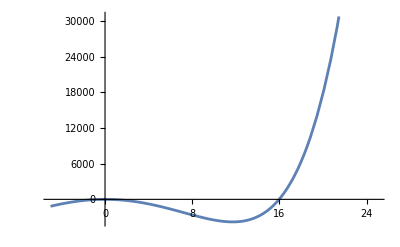

```mathematica
Plot[-m^2/2 σ^2-c/F^2 σ^6+λ/8 σ^4/.{F->6,m->10,c->-0.01,λ->1},{σ,-5,25}]
```

```mathematica
vev6[[2]]
```

```mathematica
F61=m2σ[σ]/.vevb[[2]][[1]]/.n->F/2//Simplify
```